# Model 1: Abundance Plots

This file contains the processing code for Model 1: Comparing Temporally Blind and Temporally Explicit Metrics. Before running this file, you must have extinction time and population size outputs from running Model 1 for both TPCs using Model1.nb; edit import and export locations (via ‘saveto’) for your own device. Use to generate Fig 4. (*7 Nov 2025 update: Corrected typo in beta param of TPC2 and updated color scheme + line thickness for Fig 4 (plus adjusted max/min bounds to match between species for easier comparison); fixed glitch in CD index outputs -- CDMatrixT was using p instead of pT (though graph in manuscript was already corrected from a separate file) *)

```mathematica
saveto="/SAVETO/";
```

## Load Data

Run import code before creating any figures. Edit import/export file names/locations for your local system and, if necessary, edit loaded parameter space to match your imported run. Default size is tmax2000_dims21,4,1,1000, corresponding with 1000 runs of 2000 time steps at each of 21 autocorrelation levels, 4 mean temperatures, and 1 standard deviation of temperature.

```mathematica
extTime=Import[saveto<>"extMetrics8_extTime_tmax2000_dims21,4,1,1000.m","MX"];
p=Import[saveto<>"extMetrics8_popsize_tmax2000_dims21,4,1,1000.m","MX"];

extTimeT=Import[saveto<>"extMetrics8_trop_extTime_tmax2000_dims21,4,1,1000.m","MX"];
pT=Import[saveto<>"extMetrics8_trop_popsize_tmax2000_dims21,4,1,1000.m","MX"];

tmax=2000; (*2000*)
maxsims=1000; (*1000*)
γvals=Range[0,2,.1];  (*21*)
μTvals=Range[23,26,1];  (*4*)
σTvals=Range[3,3,1]; (*1*)
```

## Calculate Temporally Blind Metrics

Calculate the expected population abundances given the means and standard deviation of temperature without any input from the simulations.

```mathematica
(*TEMPORATE - TPC1*)
gain[T_]:=Exp[-((T-TI)^2)/β];
loss[T_]:=ma Exp[mb T]+mc;
r[T_]:=(gain[T]-loss[T])/.755; 

(* Parameters of the TPC model *)
TI=29;
β=180;
ma=0.000005;
mb=0.4;
mc=0.05;

α=.001;

(*array of temperatures for each parameter set*)
W=ConstantArray[0,{Length[μTvals],Length[σTvals],tmax}];
Do[W[[i,j,k]]=InverseCDF[NormalDistribution[μTvals[[i]],σTvals[[j]]],k*(1/tmax)],{i,1,Length[μTvals]},{j,1,Length[σTvals]},{k,1,tmax-1}]
Do[W[[i,j,tmax]]=InverseCDF[NormalDistribution[μTvals[[i]],σTvals[[j]]],(tmax-.5)*(1/tmax)],{i,1,Length[μTvals]},{j,1,Length[σTvals]}];

(*set initial pop size to mean pop size for each parameter set*)
ninit=ConstantArray[0,{Length[μTvals],Length[σTvals]}];
Do[ninit[[i,k]]=(Mean[Table[r[W[[i,k,j]]],{j,1,tmax}]])/α,{k,1,Length[σTvals]},{i,1,Length[μTvals]}]
N[ninit]

l23=ConstantArray[ninit[[1]],Length[γvals]];
l23t=Transpose[{γvals,Flatten[l23]}];
l24=ConstantArray[ninit[[2]],Length[γvals]];
l24t=Transpose[{γvals,Flatten[l24]}];
l25=ConstantArray[ninit[[3]],Length[γvals]];
l25t=Transpose[{γvals,Flatten[l25]}];
l26=ConstantArray[ninit[[4]],Length[γvals]];
l26t=Transpose[{γvals,Flatten[l26]}];

(*TROPICAL - TPC2*)
gain[T_]:=Exp[-((T-TI)^2)/β];
loss[T_]:=ma Exp[mb T]+mc;
r[T_]:=(gain[T-2]-loss[T-2])/.4067; 

(* Parameters of the TPC model *)
TI=35;
β=170;
ma=0.000005;
mb=0.4;
mc=0.05;

α=.001;

(*array of temperatures for each parameter set*)
W=ConstantArray[0,{Length[μTvals],Length[σTvals],tmax}];
Do[W[[i,j,k]]=InverseCDF[NormalDistribution[μTvals[[i]],σTvals[[j]]],k*(1/tmax)],{i,1,Length[μTvals]},{j,1,Length[σTvals]},{k,1,tmax-1}]
Do[W[[i,j,tmax]]=InverseCDF[NormalDistribution[μTvals[[i]],σTvals[[j]]],(tmax-.5)*(1/tmax)],{i,1,Length[μTvals]},{j,1,Length[σTvals]}];

(*set initial pop size to mean pop size for each parameter set*)
ninit=ConstantArray[0,{Length[μTvals],Length[σTvals]}];
Do[ninit[[i,k]]=(Mean[Table[r[W[[i,k,j]]],{j,1,tmax}]])/α,{k,1,Length[σTvals]},{i,1,Length[μTvals]}]

N[ninit]

lt23=ConstantArray[ninit[[1]],Length[γvals]];
lt23t=Transpose[{γvals,Flatten[lt23]}];
lt24=ConstantArray[ninit[[2]],Length[γvals]];
lt24t=Transpose[{γvals,Flatten[lt24]}];
lt25=ConstantArray[ninit[[3]],Length[γvals]];
lt25t=Transpose[{γvals,Flatten[lt25]}];
lt26=ConstantArray[ninit[[4]],Length[γvals]];
lt26t=Transpose[{γvals,Flatten[lt26]}];
```

{{851.715},{845.332},{797.846},{691.715}}

{{589.123},{660.979},{713.579},{731.579}}

## Process Simulation Data

Given the imported extinction times and population sizes, calculate the extinction metrics (abundance, stability, and probability of extinction) and create plotting arrays.

```mathematica
(*initialize functions for calculating the proportion variance index (PV) and consecutive disparity index (CD); only the latter is computed here*)
CDindex[data_List]:=Module[{n,diffs},n=Length[data];
diffs=Abs[Log[data[[2;;]]/data[[1;;-2]]]];
Mean[diffs]]
(*PVindex[data_List]:=Module[{n,pairs,zsum},n=Length[data];
pairs=Subsets[data,{2}];
zsum=Total[(1-(Min[#]/Max[#]))&/@pairs];
(2*zsum)/(n*(n-1))]*)

(*TEMPERATE*)
meansMatrix=ConstantArray[0,{Length[γvals],Length[μTvals],maxsims}];
stdevsMatrix=ConstantArray[0,{Length[γvals],Length[μTvals],maxsims}];
stabilityMatrix=ConstantArray[0,{Length[γvals],Length[μTvals],maxsims}];
extMatrix=ConstantArray[0,{Length[γvals],Length[μTvals],maxsims}];
cdMatrix=ConstantArray[0,{Length[γvals],Length[μTvals],maxsims}];

(*averaging over all timesteps before extinction within a simulation*)
Do[If[extTime[[i,j,1,l]]<tmax,extMatrix[[i,j,l]]=1,extMatrix[[i,j,l]]=0];
meansMatrix[[i,j,l]]=Mean[p[[i,j,1,l,2;;extTime[[i,j,1,l]]]]];
stdevsMatrix[[i,j,l]]=StandardDeviation[p[[i,j,1,l,2;;extTime[[i,j,1,l]]]]];
stabilityMatrix[[i,j,l]]=meansMatrix[[i,j,l]]/stdevsMatrix[[i,j,l]],
{l,1,maxsims},{j,1,Length[μTvals]},{i,1,Length[γvals]}]

Do[cdMatrix[[i,j,l]]=CDindex[p[[i,j,1,l,2;;extTime[[i,j,1,l]]]]+.1],{l,1,maxsims},{j,1,Length[μTvals]},{i,1,Length[γvals]}]
cdMatrix2=ConstantArray[0,{Length[γvals],Length[μTvals]}];
Do[cdMatrix2[[i,j]]=DeleteAnomalies[cdMatrix[[i,j]]],
{j,1,Length[μTvals]},{i,1,Length[γvals]}] 

(*averaging across simulations with the same params*)
meansVals=ConstantArray[0,{Length[γvals],Length[μTvals]}];
meansQ1=ConstantArray[0,{Length[γvals],Length[μTvals]}];
meansQ3=ConstantArray[0,{Length[γvals],Length[μTvals]}];
stdevsVals=ConstantArray[0,{Length[γvals],Length[μTvals]}];
stabilityVals=ConstantArray[0,{Length[γvals],Length[μTvals]}];
propExt=ConstantArray[0,{Length[γvals],Length[μTvals]}];
cdVals=ConstantArray[0,{Length[γvals],Length[μTvals]}];
cdQ1=ConstantArray[0,{Length[γvals],Length[μTvals]}];
cdQ3=ConstantArray[0,{Length[γvals],Length[μTvals]}];

Do[meansVals[[i,j]]=Mean[meansMatrix[[i,j]]];
meansQ1[[i,j]]=Quantile[meansMatrix[[i,j]],.1];
meansQ3[[i,j]]=Quantile[meansMatrix[[i,j]],.9];
stdevsVals[[i,j]]=Mean[stdevsMatrix[[i,j]]];
stabilityVals[[i,j]]=Mean[stabilityMatrix[[i,j]]];
propExt[[i,j]]=Total[extMatrix[[i,j]]/maxsims];
cdVals[[i,j]]=Mean[cdMatrix2[[i,j]]];
cdQ1[[i,j]]=Quantile[cdMatrix2[[i,j]],.1];
cdQ3[[i,j]]=Quantile[cdMatrix2[[i,j]],.9],
{j,1,Length[μTvals]},{i,1,Length[γvals]}]

(*TROPICAL*)
meansMatrixT=ConstantArray[0,{Length[γvals],Length[μTvals],maxsims}];
stdevsMatrixT=ConstantArray[0,{Length[γvals],Length[μTvals],maxsims}];
stabilityMatrixT=ConstantArray[0,{Length[γvals],Length[μTvals],maxsims}];
extMatrixT=ConstantArray[0,{Length[γvals],Length[μTvals],maxsims}];
cdMatrixT=ConstantArray[0,{Length[γvals],Length[μTvals],maxsims}];

(*averaging over all timesteps before extinction within a simulation*)
Do[If[extTimeT[[i,j,1,l]]<tmax,extMatrixT[[i,j,l]]=1,extMatrixT[[i,j,l]]=0];
meansMatrixT[[i,j,l]]=Mean[pT[[i,j,1,l,2;;extTimeT[[i,j,1,l]]]]];
stdevsMatrixT[[i,j,l]]=StandardDeviation[pT[[i,j,1,l,2;;extTimeT[[i,j,1,l]]]]];
stabilityMatrixT[[i,j,l]]=meansMatrixT[[i,j,l]]/stdevsMatrixT[[i,j,l]];,
{l,1,maxsims},{j,1,Length[μTvals]},{i,1,Length[γvals]}]

Do[cdMatrixT[[i,j,l]]=CDindex[pT[[i,j,1,l,2;;extTimeT[[i,j,1,l]]]]+.1],{l,1,maxsims},{j,1,Length[μTvals]},{i,1,Length[γvals]}]
cdMatrixT2=ConstantArray[0,{Length[γvals],Length[μTvals]}];
Do[cdMatrixT2[[i,j]]=DeleteAnomalies[cdMatrixT[[i,j]]],
{j,1,Length[μTvals]},{i,1,Length[γvals]}] 

(*averaging across simulations with the same params*)
meansValsT=ConstantArray[0,{Length[γvals],Length[μTvals]}];
meansQ1T=ConstantArray[0,{Length[γvals],Length[μTvals]}];
meansQ3T=ConstantArray[0,{Length[γvals],Length[μTvals]}];
stdevsValsT=ConstantArray[0,{Length[γvals],Length[μTvals]}];
stabilityValsT=ConstantArray[0,{Length[γvals],Length[μTvals]}];
propExtT=ConstantArray[0,{Length[γvals],Length[μTvals]}];
cdValsT=ConstantArray[0,{Length[γvals],Length[μTvals]}];
cdQ1T=ConstantArray[0,{Length[γvals],Length[μTvals]}];
cdQ3T=ConstantArray[0,{Length[γvals],Length[μTvals]}];

Do[meansValsT[[i,j]]=Mean[meansMatrixT[[i,j]]];
meansQ1T[[i,j]]=Quantile[meansMatrixT[[i,j]],.1];
meansQ3T[[i,j]]=Quantile[meansMatrixT[[i,j]],.9];
stdevsValsT[[i,j]]=Mean[stdevsMatrixT[[i,j]]];
stabilityValsT[[i,j]]=Mean[stabilityMatrixT[[i,j]]];
propExtT[[i,j]]=Total[extMatrixT[[i,j]]/maxsims];
cdValsT[[i,j]]=Mean[cdMatrixT2[[i,j]]];
cdQ1T[[i,j]]=Quantile[cdMatrixT2[[i,j]],.1];
cdQ3T[[i,j]]=Quantile[cdMatrixT2[[i,j]],.9],
{j,1,Length[μTvals]},{i,1,Length[γvals]}]

(*create plotting arrays*)
means23=Transpose[{γvals,meansVals[[All,1]]}];
means24=Transpose[{γvals,meansVals[[All,2]]}];
means25=Transpose[{γvals,meansVals[[All,3]]}];
means26=Transpose[{γvals,meansVals[[All,4]]}];

means23Q1=Transpose[{γvals,meansQ1[[All,1]]}];
means23Q3=Transpose[{γvals,meansQ3[[All,1]]}];
means24Q1=Transpose[{γvals,meansQ1[[All,2]]}];
means24Q3=Transpose[{γvals,meansQ3[[All,2]]}];
means25Q1=Transpose[{γvals,meansQ1[[All,3]]}];
means25Q3=Transpose[{γvals,meansQ3[[All,3]]}];
means26Q1=Transpose[{γvals,meansQ1[[All,4]]}];
means26Q3=Transpose[{γvals,meansQ3[[All,4]]}];

cd23=Transpose[{γvals,cdVals[[All,1]]}];
cd24=Transpose[{γvals,cdVals[[All,2]]}];
cd25=Transpose[{γvals,cdVals[[All,3]]}];
cd26=Transpose[{γvals,cdVals[[All,4]]}];

cd23Q1=Transpose[{γvals,cdQ1[[All,1]]}];
cd23Q3=Transpose[{γvals,cdQ3[[All,1]]}];
cd24Q1=Transpose[{γvals,cdQ1[[All,2]]}];
cd24Q3=Transpose[{γvals,cdQ3[[All,2]]}];
cd25Q1=Transpose[{γvals,cdQ1[[All,3]]}];
cd25Q3=Transpose[{γvals,cdQ3[[All,3]]}];
cd26Q1=Transpose[{γvals,cdQ1[[All,4]]}];
cd26Q3=Transpose[{γvals,cdQ3[[All,4]]}];

propExt23=Transpose[{γvals,propExt[[All,1]]}];
propExt24=Transpose[{γvals,propExt[[All,2]]}];
propExt25=Transpose[{γvals,propExt[[All,3]]}];
propExt26=Transpose[{γvals,propExt[[All,4]]}];

means23T=Transpose[{γvals,meansValsT[[All,1]]}];
means24T=Transpose[{γvals,meansValsT[[All,2]]}];
means25T=Transpose[{γvals,meansValsT[[All,3]]}];
means26T=Transpose[{γvals,meansValsT[[All,4]]}];

means23Q1T=Transpose[{γvals,meansQ1T[[All,1]]}];
means23Q3T=Transpose[{γvals,meansQ3T[[All,1]]}];
means24Q1T=Transpose[{γvals,meansQ1T[[All,2]]}];
means24Q3T=Transpose[{γvals,meansQ3T[[All,2]]}];
means25Q1T=Transpose[{γvals,meansQ1T[[All,3]]}];
means25Q3T=Transpose[{γvals,meansQ3T[[All,3]]}];
means26Q1T=Transpose[{γvals,meansQ1T[[All,4]]}];
means26Q3T=Transpose[{γvals,meansQ3T[[All,4]]}];

cd23T=Transpose[{γvals,cdValsT[[All,1]]}];
cd24T=Transpose[{γvals,cdValsT[[All,2]]}];
cd25T=Transpose[{γvals,cdValsT[[All,3]]}];
cd26T=Transpose[{γvals,cdValsT[[All,4]]}];

cd23Q1T=Transpose[{γvals,cdQ1T[[All,1]]}];
cd23Q3T=Transpose[{γvals,cdQ3T[[All,1]]}];
cd24Q1T=Transpose[{γvals,cdQ1T[[All,2]]}];
cd24Q3T=Transpose[{γvals,cdQ3T[[All,2]]}];
cd25Q1T=Transpose[{γvals,cdQ1T[[All,3]]}];
cd25Q3T=Transpose[{γvals,cdQ3T[[All,3]]}];
cd26Q1T=Transpose[{γvals,cdQ1T[[All,4]]}];
cd26Q3T=Transpose[{γvals,cdQ3T[[All,4]]}];

propExtT23=Transpose[{γvals,propExtT[[All,1]]}];
propExtT24=Transpose[{γvals,propExtT[[All,2]]}];
propExtT25=Transpose[{γvals,propExtT[[All,3]]}];
propExtT26=Transpose[{γvals,propExtT[[All,4]]}];
```

## Create Individual Plots

Code for each individual subplot. Outputs repressed for processing time.

```mathematica
col1=Lighter[Lighter[Red]];
col2=Red;
col3=Darker[Red];
col4=Black;
wide=Thickness[0.01];

meansPlot=ListLinePlot[{means23,means23Q1,means23Q3,means24,means24Q1,means24Q3,means25,means25Q1,means25Q3,means26,means26Q1,means26Q3,l23t,l24t,l25t,l26t},PlotStyle->{{wide,col1},None,None,{wide,col2},None,None,{wide,col3},None,None,{wide,col4},None,None,{wide,Dashed,col1},{wide,Dashed,col2},{wide,Dashed,col3},{wide,Dashed,col4}},PlotRange->{{-0.02,2.02},{400,900}}, FillingStyle->Opacity[0.1],
Filling->{1->{2},1->{3},4->{5},4->{6},7->{8},7->{9},10->{11},10->{12}},
Frame->{True,True,False,False},FrameStyle->14,FrameLabel->{None(*"Spectral Exponent γ"*),"Mean Population Abundance"},LabelStyle->Directive[Black],ImageSize->500] ;(*subplot a: temp means*)

stabilityPlot=ListLinePlot[{cd26,cd26Q1,cd26Q3,cd25,cd25Q1,cd25Q3,cd24,cd24Q1,cd24Q3,cd23,cd23Q1,cd23Q3},PlotStyle->{{wide,col4},None,None,{wide,col3},None,None,{wide,col2},None,None,{wide,col1},None,None},FillingStyle->Opacity[0.1],
Filling->{10->{11},10->{12},7->{8},7->{9},4->{5},4->{6},1->{2},1->{3}},FillingStyle->Opacity[0.1],PlotRange->{{-0.02,2.02},{-.01,.55}},Frame->{True,True,False,False},FrameStyle->14,FrameLabel->{(*"Spectral Exponent γ",*)None,"Consecutive Disparity Index"},LabelStyle->Directive[Black],ImageSize->510];(*subplot b: stability*)

extinctionPlot=ListLinePlot[{propExt23,propExt24,propExt25,propExt26},PlotStyle->{{wide,col1},{wide,col2},{wide,col3},{wide,col4}},PlotRange->{{-0.02,2.02},Automatic}, Frame->{True,True,False,False},FrameStyle->14,FrameLabel->{"Spectral Exponent γ","Probability of Extinction"},LabelStyle->Directive[Black],ImageSize->500]; (*subplot c: temp extinction*)

meansPlotT=ListLinePlot[{lt23t,lt24t,lt25t,lt26t,means23T,means23Q1T,means23Q3T,means24T,means24Q1T,means24Q3T,means25T,means25Q1T,means25Q3T,means26T,means26Q1T,means26Q3T},PlotStyle->{{wide,Dashed,col1},{wide,Dashed,col2},{wide,Dashed,col3},{wide,Dashed,col4},{wide,col1},None,None,{wide,col2},None,None,{wide,col3},None,None,{wide,col4},None,None},PlotRange->{{-0.02,2.02},{400,900}}, FillingStyle->Opacity[0.1],
Filling->{5->{6},5->{7},8->{9},8->{10},11->{12},11->{13},14->{15},14->{16}},
Frame->{True,True,False,False},FrameStyle->14,(*FrameLabel->{(*None,*)"Spectral Exponent γ","Mean Population Abundance"},*)LabelStyle->Directive[Black],ImageSize->500](*subplot d: trop means*)

stabilityPlotT=ListLinePlot[{cd23T,cd23Q1T,cd23Q3T,cd24T,cd24Q1T,cd24Q3T,cd25T,cd25Q1T,cd25Q3T,cd26T,cd26Q1T,cd26Q3T},PlotStyle->{{wide,col1},None,None,{wide,col2},None,None,{wide,col3},None,None,{wide,col4},None,None},PlotRange->{{-0.02,2.02},{-.01,.55}}, FillingStyle->Opacity[0.1],
(*PlotLabel->Style["Specialist",16],*)
Filling->{10->{11},10->{12},7->{8},7->{9},4->{5},4->{6},1->{2},1->{3}},Frame->{True,True,False,False},FrameStyle->14,(*FrameLabel->{None(*"Spectral Exponent γ"*),"Population Stability"},*)LabelStyle->Directive[Black],ImageSize->510];(*subplot e: trop stability*)

extinctionPlotT=ListLinePlot[{propExtT23,propExtT24,propExtT25,propExtT26},PlotStyle->{{wide,col1},{wide,col2},{wide,col3},{wide,col4}},PlotRange->{{-0.02,2.02},Automatic}, Frame->{True,True,False,False},FrameStyle->14,FrameLabel->{"Spectral Exponent γ",None(*"Probability of Extinction"*)},LabelStyle->Directive[Black],ImageSize->500];(*subplot f: trop extinction*)
```

## Fig 4: Extinction Metrics

Create Fig 4. Labeling added in Adobe Illustrator 2024.

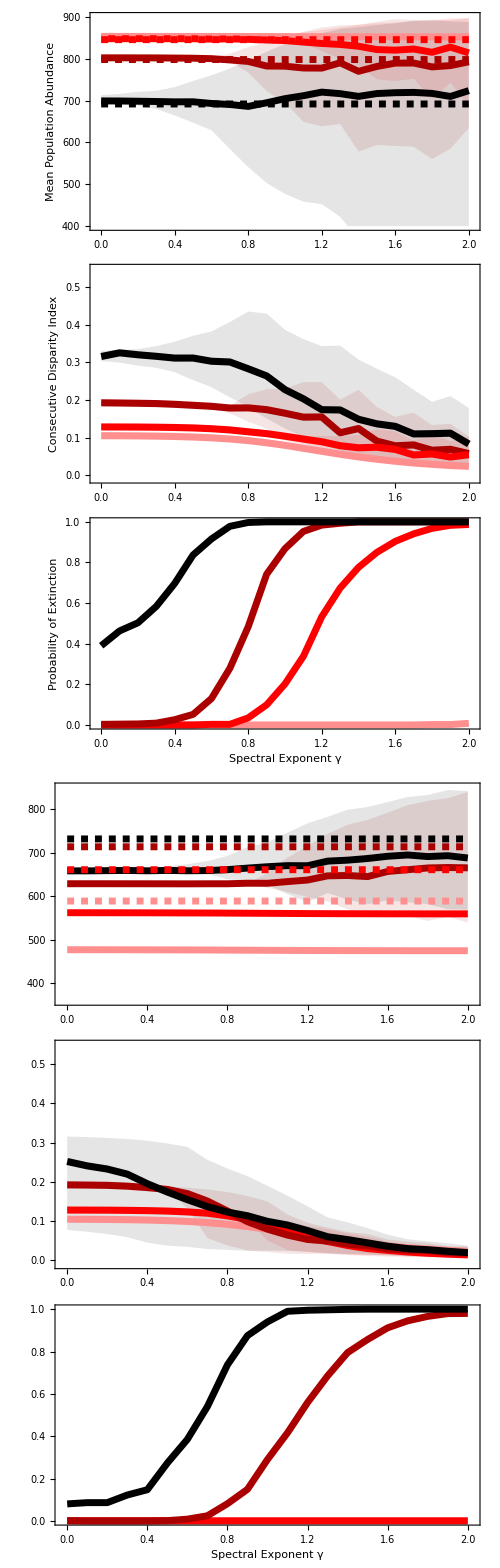

```mathematica
fig4=GraphicsColumn[{meansPlot,stabilityPlot,extinctionPlot,meansPlotT,stabilityPlotT,extinctionPlotT},Spacings->{0,0},ImageSize->500];
(*fig4=GraphicsGrid[{{meansPlot,meansPlotT},{stabilityPlot,stabilityPlotT},{extinctionPlot,extinctionPlotT}},Spacings->{0,0},ImageSize->1000]*)

Export[saveto<>"Figure4.pdf",fig4,ImageResolution->1000];
(*Export[saveto<>"meansPlot.pdf",meansPlot,ImageResolution->1000]
Export[saveto<>"meansPlotT.pdf",meansPlotT,ImageResolution->1000]
Export[saveto<>"stabilityPlot.pdf",stabilityPlot,ImageResolution->1000]
Export[saveto<>"stabilityPlotT.pdf",stabilityPlotT,ImageResolution->1000]
Export[saveto<>"extinctionPlot.pdf",extinctionPlot,ImageResolution->1000]
Export[saveto<>"extinctionPlotT.pdf",extinctionPlotT,ImageResolution->1000]*)
```